```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F12"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F12\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,30]
,15,0.000001],1500<#[[1]]<6000&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],30],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],30]
,15,0.000001],1500<#[[1]]<6000&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,22},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.010,0.02},{0.8,1}},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::ivar: 1 is not a valid variable.

General::ivar: 2 is not a valid variable.

General::ivar: 3 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
power[[46]]
```

15

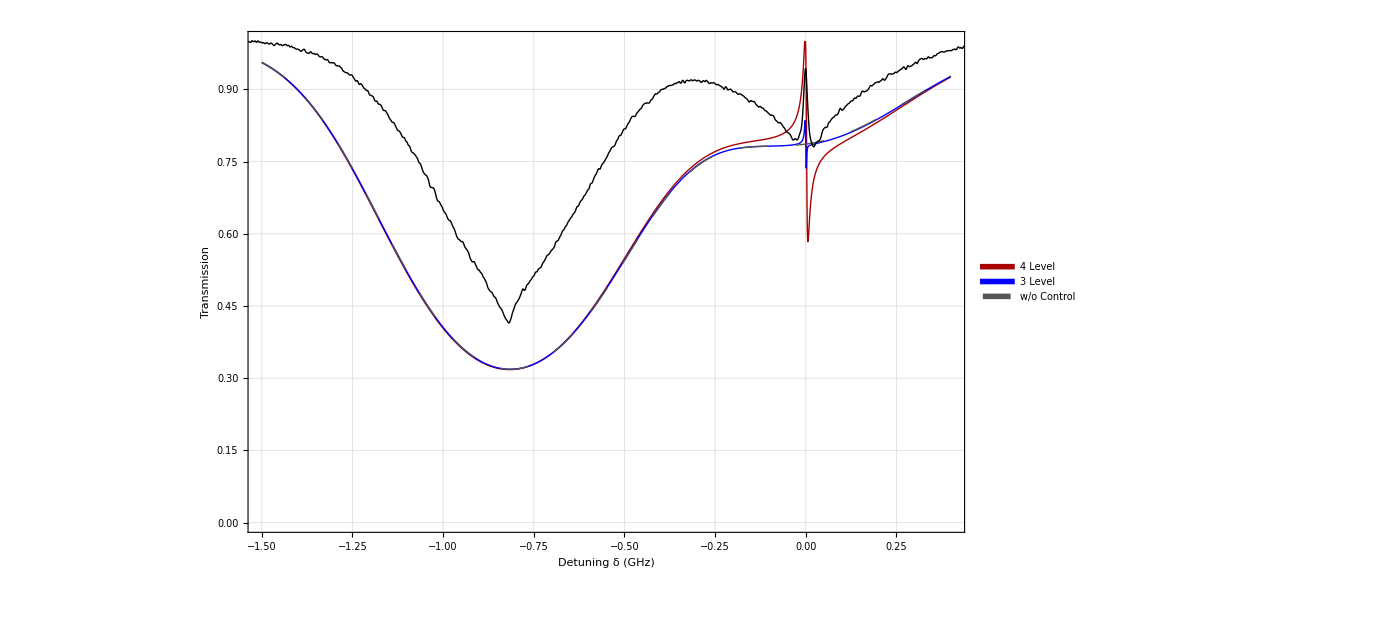

```mathematica
final2=ListPlot[{Lev4DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Blue},{AbsoluteThickness[1],Darker[Gray],Dashing[.02]},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-1.5,0.4},{0.0,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax8712=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0<#[[1]]<0.01&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&][[All,2]]//Max],{i,1,Length[data],1}];
EITmin8712=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0<#[[1]]<0.01&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&][[All,2]]//Min],{i,1,Length[data],1}];
```

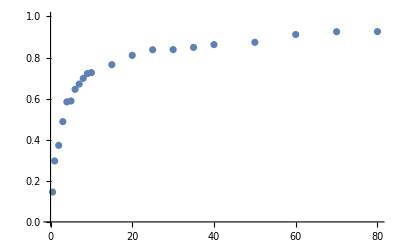

```mathematica
rb8712=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax8712,4]]/Log[Min/@Partition[EITmin8712,4]]}]},PlotRange->{0,1}]
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.02&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.808096

```mathematica
halfv8712=EITmin8712+(EITmax8712-EITmin8712)/2
```

{0.863939,0.861342,0.860323,0.861273,0.857145,0.857725,0.842927,0.860687,0.851202,0.850726,0.852584,0.8535,0.851969,0.853038,0.849915,0.8514,0.858615,0.857255,0.85148,0.852633,0.858182,0.856904,0.857173,0.85619,0.860412,0.861145,0.856939,0.860709,0.858603,0.857436,0.85786,0.86284,0.860624,0.858758,0.850213,0.858707,0.861944,0.857285,0.857536,0.857026,0.85909,0.860308,0.859456,0.862229,0.862437,0.858331,0.858132,0.86024,0.85737,0.860118,0.859673,0.858064,0.858863,0.857601,0.855632,0.857346,0.860357,0.858113,0.8572,0.854631,0.848407,0.85713,0.853909,0.85345,0.85715,0.857793,0.850541,0.858432,0.847889,0.847808,0.846329,0.844266,0.867625,0.848253,0.872216,0.862955,0.861215,0.839259,0.869893,0.857164,0.885148,0.861944,0.834131,0.870244}

```mathematica
Manipulate[
Which[i≤14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.01&];,
45>=i>14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&];,
i>45,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.02&];

];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv8712[[i]],If[i==54∨i==58∨i==60∨i==61∨i==77∨i==83,10,5]];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
Show[ListPlot[{ddd,ddd1},PlotStyle->{Black,{Blue,AbsolutePointSize[8]}},Epilog->Line[{{-1,halfv8712[[i]]},{1,halfv8712[[i]]}}]],Plot[{f1,f2},{x,-2,1},PlotRange->{0,1},PlotStyle->{{Red,Dashed},{Red,Dashed}}]]
,{i,1,Length[data2],1}]
Abs[Solve[f1==halfv8712[[1]],x][[1,1,2]]-Solve[f2==halfv8712[[1]],x][[1,1,2]]]*10^3(*in MHz*)
```

0.588082

```mathematica
fff={};
```

```mathematica
Do[
Which[i≤14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.01&];,
45>=i>14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&];,
i>45,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.02&];

];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv8712[[i]],If[i==54∨i==58∨i==60∨i==61∨i==77∨i==83,20,5]];
ddd1=ddd[[Sort[Flatten[pos]]]];
fff=Append[fff,ddd1];

,{i,1,Length[data2],1}]
```

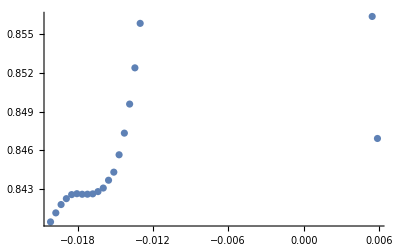

```mathematica
ListPlot[fff[[61]],PlotRange->All]
```

```mathematica
kkk={};
Do[
cc=ClusterClassify[fff[[i]],Method->"DBSCAN"];
kkk=Append[kkk,Mean/@GatherBy[fff[[i]],cc]]
,{i,1,Length[data2],1}]
```

```mathematica
Manipulate[kkk[[i]],{i,1,Length[data2],1}]
```

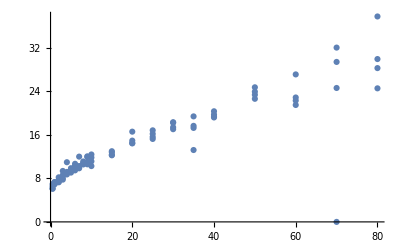

```mathematica
ListPlot[Transpose[{power,Table[Abs[kkk[[i,1,1]]-kkk[[i,-1,1]]]*1000,{i,1,Length[data2],1}]}],PlotRange->All]
```

```mathematica
Transpose[{power,Table[Abs[kkk[[i,1,1]]-kkk[[i,-1,1]]]*1000,{i,1,Length[data2],1}]}]
```

{{0.5,6.11789},{0.5,6.94737},{0.5,6.11157},{0.5,6.53981},{1,7.30809},{1,6.94021},{1,6.99792},{1,7.31932},{2,7.73757},{2,8.19784},{2,7.28571},{2,7.37603},{3,7.77743},{3,9.37213},{3,8.0708},{3,8.6138},{4,10.9766},{4,8.7295},{4,8.9877},{4,9.18731},{5,9.45417},{5,9.87436},{5,9.41538},{5,9.07135},{6,10.6872},{6,10.3158},{6,9.47858},{6,10.1072},{7,9.85913},{7,10.1792},{7,10.2628},{7,12.0062},{8,10.5624},{8,10.7813},{8,11.112},{8,10.7258},{9,11.9445},{9,10.5947},{9,12.056},{9,11.027},{10,11.1406},{10,12.4019},{10,10.2681},{10,11.8411},{15,13.0015},{15,12.3383},{15,12.7959},{15,12.2504},{20,14.4369},{20,14.5113},{20,14.9518},{20,16.5987},{25,16.197},{25,16.8421},{25,15.6362},{25,15.2582},{30,17.0526},{30,18.2346},{30,17.4108},{30,18.3371},{35,13.2222},{35,17.2864},{35,19.4087},{35,17.6668},{40,20.3486},{40,19.2122},{40,19.7554},{40,19.379},{50,23.951},{50,22.6436},{50,24.7583},{50,23.3805},{60,22.8843},{60,27.1299},{60,21.5067},{60,22.319},{70,0.},{70,32.0616},{70,24.6332},{70,29.4261},{80,24.5682},{80,29.9544},{80,37.7893},{80,28.2897}}

```mathematica
rb87w12={{0.5,6.117890382626667},{0.5,6.947368421052591},{0.5,6.1115702479339244},{0.5,6.5398138572904845},{1,7.308085977482041},{1,6.9402061855670105},{1,6.997920997920996},{1,7.31932342388512},{2,7.7375704766786315},{2,8.197836166924265},{2,7.2857142857143025},{2,7.37603305785121},{3,7.777434312210119},{3,9.372128637059717},{3,8.070796460177018},{3,8.613800205973355},{4,10.976649746192873},{4,8.729495669893042},{4,8.9877049180328},{4,9.187308085977453},{5,9.454170957775528},{5,9.874356333676616},{5,9.415384615384566},{5,9.071354705274093},{6,10.68721109399066},{6,10.315789473684204},{6,9.478575116159053},{6,10.107178968655168},{7,9.859125964010211},{7,10.179226069246445},{7,10.262833675564686},{7,12.006195147134784},{8,10.562436548223346},{8,10.781347150259247},{8,11.112024665981528},{8,10.72577319587631},{9,11.944530046224976},{9,10.594704684317707},{9,12.055987558320417},{9,11.027027027026959},{10,11.140649149922632},{10,12.401854714064964},{10,10.268104776579356},{10,11.841140529531483},{15,13.001517450682824},{15,12.33828805740637},{15,12.795886889460132},{15,12.2503816793893},{20,14.436923076923161},{20,14.511340206185533},{20,14.951807228915685},{20,16.59869412355604},{25,16.19698492462318},{25,16.842105263157855},{25,15.636177823198851},{25,15.258196721311567},{30,17.052631578947395},{30,18.234636871508442},{30,17.41079691516704},{30,18.33707865168527},{35,13.22222222222226},{35,17.286370597243415},{35,19.408695652174014},{35,17.66683647478351},{40,20.348614609571825},{40,19.212151898734152},{40,19.755351681957244},{40,19.37895812053125},{50,23.950995405819352},{50,22.64358452138493},{50,24.758274824473347},{50,23.38048528652553},{60,22.884284992420344},{60,27.129896907216565},{60,21.50665301944732},{60,22.31901840490813},{70,0.},{70,32.061633281972256},{70,24.633181126331838},{70,29.4260869565216},{80,24.568193515182745},{80,29.95443037974682},{80,37.78931297709928},{80,28.289676425269693}}
```

{{0.5,6.11789},{0.5,6.94737},{0.5,6.11157},{0.5,6.53981},{1,7.30809},{1,6.94021},{1,6.99792},{1,7.31932},{2,7.73757},{2,8.19784},{2,7.28571},{2,7.37603},{3,7.77743},{3,9.37213},{3,8.0708},{3,8.6138},{4,10.9766},{4,8.7295},{4,8.9877},{4,9.18731},{5,9.45417},{5,9.87436},{5,9.41538},{5,9.07135},{6,10.6872},{6,10.3158},{6,9.47858},{6,10.1072},{7,9.85913},{7,10.1792},{7,10.2628},{7,12.0062},{8,10.5624},{8,10.7813},{8,11.112},{8,10.7258},{9,11.9445},{9,10.5947},{9,12.056},{9,11.027},{10,11.1406},{10,12.4019},{10,10.2681},{10,11.8411},{15,13.0015},{15,12.3383},{15,12.7959},{15,12.2504},{20,14.4369},{20,14.5113},{20,14.9518},{20,16.5987},{25,16.197},{25,16.8421},{25,15.6362},{25,15.2582},{30,17.0526},{30,18.2346},{30,17.4108},{30,18.3371},{35,13.2222},{35,17.2864},{35,19.4087},{35,17.6668},{40,20.3486},{40,19.2122},{40,19.7554},{40,19.379},{50,23.951},{50,22.6436},{50,24.7583},{50,23.3805},{60,22.8843},{60,27.1299},{60,21.5067},{60,22.319},{70,0.},{70,32.0616},{70,24.6332},{70,29.4261},{80,24.5682},{80,29.9544},{80,37.7893},{80,28.2897}}